```mathematica
(* This notebook simulates the small open economy model in the handout TractableBufferStock associated 
with Christopher Carroll's first year graduate macroeconomics course; see that document for notation and explanations *)
```

```mathematica
(* This cell is basically housekeeping and setup stuff; it can be ignored *)
ClearAll["Global`*"];ParamsAreSet=False;
If[$VersionNumber<8,(*then*) Print["These programs require Mathematica version 8 or greater."];Abort[]];
If[Length[$FrontEnd] > 0,NBDir=SetDirectory[NotebookDirectory[]]];(* If running from the Notebook interface *)
rootDir = SetDirectory["../../.."];
AutoLoadDir=SetDirectory["./Mathematica/CoreCode/Autoload"];Get["./init.m"];
CoreCodeDir=SetDirectory[".."];
rootDir = SetDirectory[".."];
Get[CoreCodeDir<>"/MakeAnalyticalResults.m"];
Get[CoreCodeDir<>"/VarsAndFuncs.m"];
(* Method of creating figures depends on whether being run in batch mode or interactively *)
If[$FrontEnd == Null,OpenFigsUsingShell=True,OpenFigsUsingShell=False];
```

```mathematica
Get[CoreCodeDir<>"/ParametersBase.m"];
FindStableArm;
```

Solving ...

Below 𝓂MinPermitted after 63 backwards Euler iterations.

Last 2 Points:(0.824412 | 0.342591 | 0.330215 | -21.6355 | -0.203069
-0.0283241 | 0.143006 | -2.10391 | -19.4339 | -81.0262)

Solving ...

Above 𝓂MaxPermitted after 119 backwards Euler iterations.

Last 2 Points:(97.6944 | 7.47043 | 0.062828 | -2.17971 | -0.0000302828
102.097 | 7.74672 | 0.0627009 | -2.10364 | -0.0000275432)

```mathematica
SetDirectory[NotebookDirectory[]];
<<SOESimFuncs.m;
<<SOESimParams.m;
```

```mathematica
(* Don't worry about the error messages this generates *)
VerboseOutput=False;CensusMakeStakes;
Do[AddNewGen[{𝒷E,𝒩,𝔊}],{4}];
ϑ=0.06;
FindStableArm;
```

Interpolation::inhr: Requested order is too high; order has been reduced to {0}.

InterpolatingFunction::dmval: Input value {4.5695} lies outside the range of data in the interpolating function. Extrapolation will be used.

```mathematica
Do[AddNewGen[{𝒷E,𝒩,𝔊}],{75}];
```

InterpolatingFunction::dmval: Input value {7.85446} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {8.1493} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction :: dmval will be suppressed during this calculation.

```mathematica
timePath=Table[i,{i,Length[CensusMeans]}];
cPathAfterThetaDropPlot=ListPlot[Transpose[{timePath,CensusMeansT[[𝒸Pos]]}],PlotRange->All,PlotStyle->Black];
```

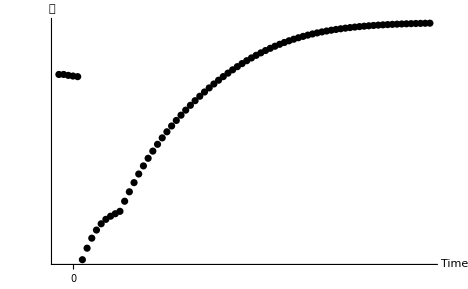

Exporting figure to /Volumes/Data/Courses/Choice/LectureNotes/Consumption/Handouts/TractableBufferStock/Code/Mathematica/Examples/TractableBufferStock/Figures/SOEStakescPathAfterThetaDropPlot.xxx

-Graphics-

```mathematica
SOEStakescPathAfterThetaDropPlot=Show[cPathAfterThetaDropPlot,Ticks->{{{4,"0"}},None},AxesLabel->{"Time","𝒸"},AxesOrigin->{-3,0},PlotRange->{{-3,Automatic},{0,Automatic}}];
ExportFigsToDir["SOEStakescPathAfterThetaDropPlot","/Volumes/Data/Courses/Choice/LectureNotes/Consumption/Handouts/TractableBufferStock/Code/Mathematica/Examples/TractableBufferStock/Figures"];
Show[SOEStakescPathAfterThetaDropPlot]
```

Interpolation::inhr: Requested order is too high; order has been reduced to {0}.

InterpolatingFunction::dmval: Input value {7.92185} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction :: dmval will be suppressed during this calculation.

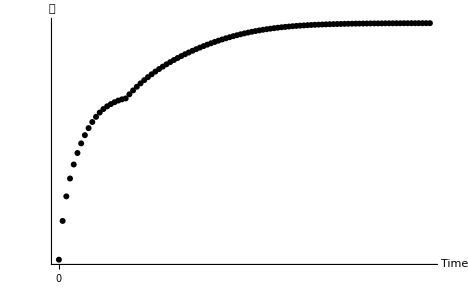

Exporting figure to /Volumes/Data/Courses/Choice/LectureNotes/Consumption/Handouts/TractableBufferStock/Code/Mathematica/Examples/TractableBufferStock/Figures/SOENoStakescPath.xxx

-Graphics-

```mathematica
CensusMakeNoStakes;
VerboseOutput=False;
Do[AddNewGen[{0,𝒩,𝔊}],{100}];
timePath=Table[i,{i,Length[Census]}];
cPath=ListPlot[Transpose[{timePath,CensusMeansT[[𝒸Pos]]}],PlotRange->All];

SOENoStakescPath=Show[cPath,Ticks->{{{1,"0"}},None},AxesLabel->{"Time","𝒸"},AxesOrigin->{-3,0},PlotRange->{{-3,All},{0,All}}];
ExportFigsToDir["SOENoStakescPath","/Volumes/Data/Courses/Choice/LectureNotes/Consumption/Handouts/TractableBufferStock/Code/Mathematica/Examples/TractableBufferStock/Figures"];
Show[SOENoStakescPath]
```